Alle 10 Wurzeln von 9+8 ⅈ:

{x→-1.27915-0.0931123 ⅈ}
{x→-1.08958+0.676535 ⅈ}
{x→-0.980123-0.827194 ⅈ}
{x→-0.483834+1.18777 ⅈ}
{x→-0.306723-1.24532 ⅈ}
{x→0.306723+1.24532 ⅈ}
{x→0.483834-1.18777 ⅈ}
{x→0.980123+0.827194 ⅈ}
{x→1.08958-0.676535 ⅈ}
{x→1.27915+0.0931123 ⅈ}

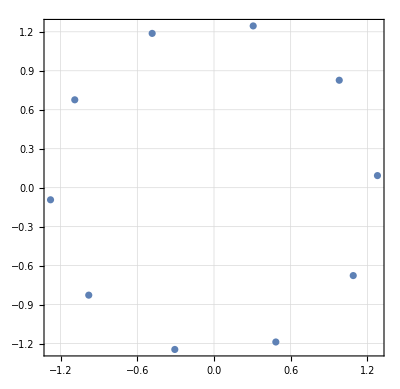

Summe aller Wurzeln:

0.+4.44089×10^-16 ⅈ

Alle positiven Wurzeln:

0.306723+1.24532 ⅈ
0.980123+0.827194 ⅈ
1.27915+0.0931123 ⅈ

Summe aller positiven Wurzeln:

2.56599+2.16562 ⅈ

```mathematica
z = 9+8I;
n = 10;
Clist = NSolve[x^n == z,x];
Print[StringForm["Alle `1` Wurzeln von `2`:",n,z]]
Column[Clist]
numeric = Clist[[All,1,2]] ;
ComplexListPlot[numeric,PlotTheme->"Detailed"]
Print["Summe aller Wurzeln:"]


Total[numeric]
positive =Select[numeric, Re[#]>0 && Im[#]>0&] ;
Print["Alle positiven Wurzeln:"]
Column[positive]
Print["Summe aller positiven Wurzeln:"]
Total[positive]
```